# WDBC Benign/Malignant Tumor Class Predictor

## System Requirements

Mathematica, version 7 or higher

Computational Intelligence Packages (CIP), version 1.2 or higher (available at http://www.gnwi.de)

## Task Description

Construction of a minimal benign/malignant tumor class predictor model for the Wisconsin Diagnostic Breast Cancer (WDBC) data.

## Data source

Wisconsin Diagnostic Breast Cancer (WDBC) data set. Taken at 2011/01/30 from the UCI (University of California at Irvine) machine learning repository at http://archive.ics.uci.edu/ml. Repository citation: A. Frank, A. Asuncion (2010), UCI Machine Learning Repository (http://archive.ics.uci.edu/ml), Irvine, CA: University of California, School of Information and Computer Science. First citation in medical literature: W.H. Wolberg,W.N. Street, and O.L.Mangasarian, Machine learning techniques to diagnose breast cancer from fine-needle aspirates, Cancer Letters 77 (1994), 163-171.

The WDBC data are available from the CIP ExperimentalData package.

```mathematica
<<CIP`ExperimentalData`
```

```mathematica
wdbcDataSet=CIP`ExperimentalData`GetWDBCClassificationDataSet[];
```

## Data inspection

```mathematica
<<CIP`Graphics`
```

```mathematica
CIP`Graphics`ShowDataSetInfo[{"IoPairs","InputComponents","OutputComponents","ClassCount"},wdbcDataSet]
```

Number of IO pairs = 569

Number of input components = 30

Number of output components = 2

Class 1 with 357 members

Class 2 with 212 members

Output class assignment:
Class 1: Benign tumors.
Class 2: Malignant tumors

Remarks:
Number of class 1 members considerably exceeds number of class 2 members.

## Unsupervised Learning: Clustering-based Class Predictor

```mathematica
<<CIP`Cluster`
```

### Full WDBC data set

85.4% correct classifications

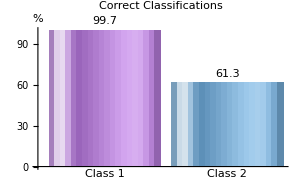

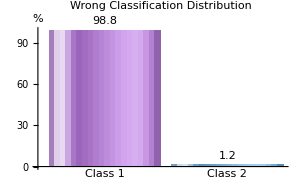

```mathematica
clusterInfo=CIP`Cluster`FitCluster[wdbcDataSet];
CIP`Cluster`ShowClusterSingleClassification[{"CorrectClassification","CorrectClassificationPerClass","WrongClassificationDistribution"},wdbcDataSet,clusterInfo]
```

Remarks:
Predictive success for malignant class 2 tumors is poor.

## Supervised Learning: Linear Approach with MLR

```mathematica
<<CIP`MLR`
```

### Full WDBC data set

96.5% correct classifications

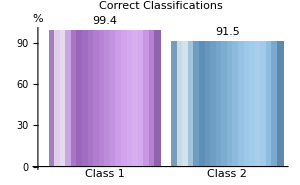

```mathematica
mlrInfo=CIP`MLR`FitMlr[wdbcDataSet];
CIP`MLR`ShowMlrSingleClassification[{"CorrectClassification","CorrectClassificationPerClass"},wdbcDataSet,mlrInfo]
```

Remarks:
Considerable improvement in comparison to unsupervised learning is achieved.

### Minimal set of input features

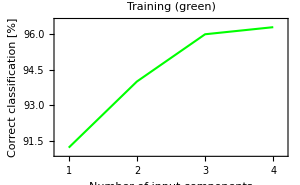

Input component list = {28,21,22,24}

```mathematica
trainingAndTestSet={wdbcDataSet,{}};
numberOfInclusionsPerStepList=Table[1,{4}];
mlrInputComponentRelevanceListForClassification=CIP`MLR`GetMlrInputInclusionClass[trainingAndTestSet,UtilityOptionsInclusionsPerStep->numberOfInclusionsPerStepList];
CIP`MLR`ShowMlrInputRelevanceClass[mlrInputComponentRelevanceListForClassification]
```

```mathematica
inputComponentInclusionList={28,21,22,24};
reducedWdbcDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[wdbcDataSet,inputComponentInclusionList];
```

Remarks:
Predictive success of the reduced set with only 4 input features is comparable to full set.

### Training/test set partitioning for reduced WDBC data set

Training Set:

96.1% correct classifications

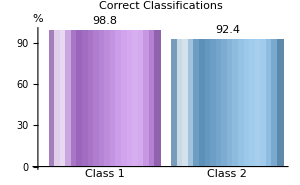

Test Set:

96.5% correct classifications

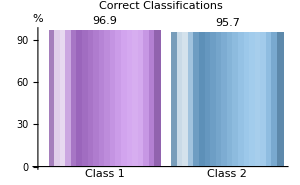

```mathematica
trainingFraction=0.5;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
mlrTrainOptimization=CIP`MLR`GetMlrTrainOptimization[reducedWdbcDataSet,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength -> blackListLength];

bestOptimization="MinimumDeviation";
bestIndex=CIP`MLR`GetBestMlrClassOptimization[mlrTrainOptimization,UtilityOptionsBestOptimization->bestOptimization];

trainingAndTestSet=mlrTrainOptimization[[3,bestIndex]];
mlrInfo=mlrTrainOptimization[[4,bestIndex]];
CIP`MLR`ShowMlrClassificationResult[{"CorrectClassification","CorrectClassificationPerClass"},trainingAndTestSet,mlrInfo]
```

Remarks:
The predictive success of the test set is comparable to the training set: No overfitting.

## Supervised Learning: Non-linear Polynomial Approach with MPR

```mathematica
<<CIP`MPR`
```

### Parabolic approach

```mathematica
polynomialDegree=2;
```

#### Full WDBC data set

```mathematica
mprInfo=CIP`MPR`FitMpr[wdbcDataSet,polynomialDegree];
CIP`MPR`ShowMprSingleClassification[{"CorrectClassification"},wdbcDataSet,mprInfo]
```

100.% correct classifications

Remarks:
Perfect 100% classification indicates unwanted overfitting.

#### Training/test set partitioning for full WDBC data set

```mathematica
trainingFraction=0.5;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
mprTrainOptimization=CIP`MPR`GetMprTrainOptimization[wdbcDataSet,polynomialDegree,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength -> blackListLength];

bestOptimization="MinimumDeviation";
bestIndex=CIP`MPR`GetBestMprClassOptimization[mprTrainOptimization,UtilityOptionsBestOptimization->bestOptimization];

trainingAndTestSet=mprTrainOptimization[[3,bestIndex]];
mprInfo=mprTrainOptimization[[4,bestIndex]];
CIP`MPR`ShowMprClassificationResult[{"CorrectClassification"},trainingAndTestSet,mprInfo]
```

Training Set:

100.% correct classifications

Test Set:

80.4% correct classifications

Remarks:
Overfitting is validated by poor test set result in comparison to perfect 100% training.

#### Minimal set of input features

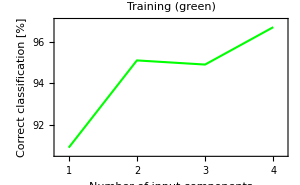

Input component list = {24,28,21,22}

```mathematica
trainingAndTestSet={wdbcDataSet,{}};
numberOfInclusionsPerStepList=Table[1,{4}];
mprInputComponentRelevanceListForClassification=CIP`MPR`GetMprInputInclusionClass[trainingAndTestSet,polynomialDegree,UtilityOptionsInclusionsPerStep-> numberOfInclusionsPerStepList];
CIP`MPR`ShowMprInputRelevanceClass[mprInputComponentRelevanceListForClassification]
```

```mathematica
inputComponentInclusionList={24,28,21,22};
reducedWdbcDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[wdbcDataSet,inputComponentInclusionList];
```

#### Training/test set partitioning for reduced WDBC data set

Training Set:

96.1% correct classifications

-Graphics-

Test Set:

96.5% correct classifications

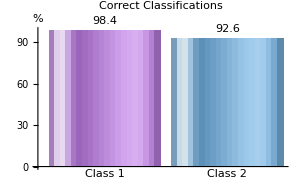

```mathematica
trainingFraction=0.5;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
mprTrainOptimization=CIP`MPR`GetMprTrainOptimization[reducedWdbcDataSet,polynomialDegree,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength -> blackListLength];

bestOptimization="MinimumDeviation";
bestIndex=CIP`MPR`GetBestMprClassOptimization[mprTrainOptimization,UtilityOptionsBestOptimization->bestOptimization];

trainingAndTestSet=mprTrainOptimization[[3,bestIndex]];
mprInfo=mprTrainOptimization[[4,bestIndex]];
CIP`MPR`ShowMprClassificationResult[{"CorrectClassification","CorrectClassificationPerClass"},trainingAndTestSet,mprInfo]
```

Remarks:
No overfitting.
Predictive success is comparable to linear MLR approach.

### Cubic approach

```mathematica
polynomialDegree=3;
```

#### Minimal set of input features

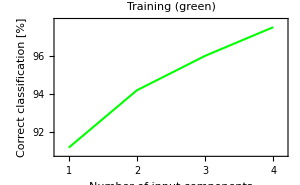

Input component list = {28,24,21,22}

```mathematica
trainingAndTestSet={wdbcDataSet,{}};
numberOfInclusionsPerStepList=Table[1,{4}];
mprInputComponentRelevanceListForClassification=CIP`MPR`GetMprInputInclusionClass[trainingAndTestSet,polynomialDegree,UtilityOptionsInclusionsPerStep->numberOfInclusionsPerStepList];
CIP`MPR`ShowMprInputRelevanceClass[mprInputComponentRelevanceListForClassification]
```

```mathematica
inputComponentInclusionList={28,24,21,22};
reducedWdbcDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[wdbcDataSet,inputComponentInclusionList];
```

#### Training/test set partitioning for reduced WDBC data set

Training Set:

96.8% correct classifications

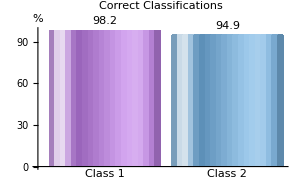

Test Set:

96.8% correct classifications

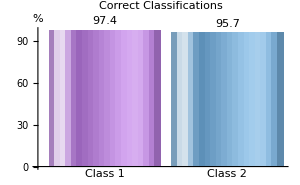

```mathematica
trainingFraction=0.5;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
mprTrainOptimization=CIP`MPR`GetMprTrainOptimization[reducedWdbcDataSet,polynomialDegree,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength->blackListLength];

bestOptimization="MinimumDeviation";
bestIndex=CIP`MPR`GetBestMprClassOptimization[mprTrainOptimization,UtilityOptionsBestOptimization->bestOptimization];

trainingAndTestSet=mprTrainOptimization[[3,bestIndex]];
mprInfo=mprTrainOptimization[[4,bestIndex]];
CIP`MPR`ShowMprClassificationResult[{"CorrectClassification","CorrectClassificationPerClass"},trainingAndTestSet,mprInfo]
```

Remarks:
No overfitting.
Predictive success is slightly superior to linear MLR and parabolic MPR approach.

## Supervised Learning: Non-linear Approach with 3L-FF Neural Networks (Perceptrons)

```mathematica
<<CIP`Perceptron`
```

### 3 hidden neurons (3-HN)

```mathematica
numberOfHiddenNeurons=3;
```

#### Minimal set of input features

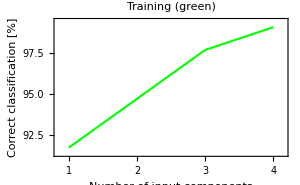

Input component list = {23,28,22,26}

```mathematica
trainingAndTestSet={wdbcDataSet,{}};
numberOfInclusionsPerStepList=Table[1,{4}];
perceptronInputComponentRelevanceListForClassification=CIP`Perceptron`GetPerceptronInputInclusionClass[trainingAndTestSet,numberOfHiddenNeurons,UtilityOptionsInclusionsPerStep->numberOfInclusionsPerStepList];
CIP`Perceptron`ShowPerceptronInputRelevanceClass[perceptronInputComponentRelevanceListForClassification]
```

```mathematica
inputComponentInclusionList={23,28,22,26};
reducedWdbcDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[wdbcDataSet,inputComponentInclusionList];
```

#### Training/test set partitioning for reduced WDBC data set

Training Set:

97.9% correct classifications

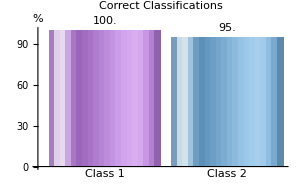

Test Set:

97.9% correct classifications

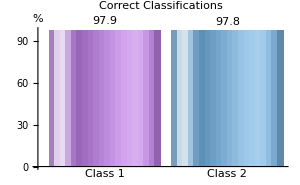

```mathematica
trainingFraction=0.5;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
perceptronTrainOptimization=CIP`Perceptron`GetPerceptronTrainOptimization[reducedWdbcDataSet,numberOfHiddenNeurons,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength->blackListLength];

bestOptimization="MinimumDeviation";
bestIndex=CIP`Perceptron`GetBestPerceptronClassOptimization[perceptronTrainOptimization,UtilityOptionsBestOptimization->bestOptimization];

trainingAndTestSet=perceptronTrainOptimization[[3,bestIndex]];
perceptronInfo=perceptronTrainOptimization[[4,bestIndex]];
CIP`Perceptron`ShowPerceptronClassificationResult[{"CorrectClassification","CorrectClassificationPerClass"},trainingAndTestSet,perceptronInfo]
```

Remarks:
No overfitting.
Predictive success is slightly superior to cubic MPR approach.

### 5 hidden neurons (5-HN)

```mathematica
numberOfHiddenNeurons=5;
```

#### Minimal set of input features

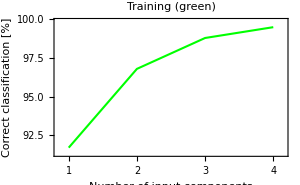

Input component list = {23,25,22,19}

```mathematica
trainingAndTestSet={wdbcDataSet,{}};
numberOfInclusionsPerStepList=Table[1,{4}];
perceptronInputComponentRelevanceListForClassification=CIP`Perceptron`GetPerceptronInputInclusionClass[trainingAndTestSet,numberOfHiddenNeurons,UtilityOptionsInclusionsPerStep->numberOfInclusionsPerStepList];
CIP`Perceptron`ShowPerceptronInputRelevanceClass[perceptronInputComponentRelevanceListForClassification]
```

```mathematica
inputComponentInclusionList={23,25,22,19};
reducedWdbcDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[wdbcDataSet,inputComponentInclusionList];
```

#### Training/test set partitioning for reduced WDBC data set

Training Set:

98.2% correct classifications

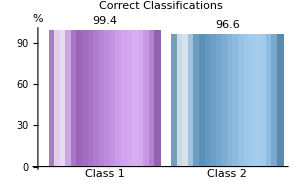

Test Set:

98.2% correct classifications

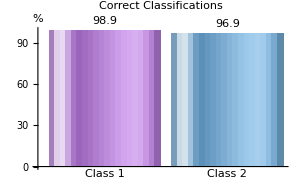

```mathematica
trainingFraction=0.5;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
perceptronTrainOptimization=CIP`Perceptron`GetPerceptronTrainOptimization[reducedWdbcDataSet,numberOfHiddenNeurons,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength->blackListLength];

bestOptimization="MinimumDeviation";
bestIndex=CIP`Perceptron`GetBestPerceptronClassOptimization[perceptronTrainOptimization,UtilityOptionsBestOptimization->bestOptimization];

trainingAndTestSet=perceptronTrainOptimization[[3,bestIndex]];
perceptronInfo=perceptronTrainOptimization[[4,bestIndex]];
CIP`Perceptron`ShowPerceptronClassificationResult[{"CorrectClassification","CorrectClassificationPerClass"},trainingAndTestSet,perceptronInfo]
```

Remarks:
No overfitting.
Predictive success is slightly superior to 3-hidden-neuron (3-HN) perceptron approach.

### 7 hidden neurons (7-HN)

```mathematica
numberOfHiddenNeurons=7;
```

#### Minimal set of input features

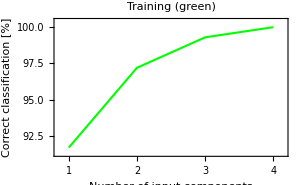

Input component list = {23,28,22,14}

```mathematica
trainingAndTestSet={wdbcDataSet,{}};
numberOfInclusionsPerStepList=Table[1,{4}];
perceptronInputComponentRelevanceListForClassification=CIP`Perceptron`GetPerceptronInputInclusionClass[trainingAndTestSet,numberOfHiddenNeurons,UtilityOptionsInclusionsPerStep->numberOfInclusionsPerStepList];
CIP`Perceptron`ShowPerceptronInputRelevanceClass[perceptronInputComponentRelevanceListForClassification]
```

```mathematica
inputComponentInclusionList={23,28,22,14};
reducedWdbcDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[wdbcDataSet,inputComponentInclusionList];
```

#### Training/test set partitioning for reduced WDBC data set

Training Set:

98.9% correct classifications

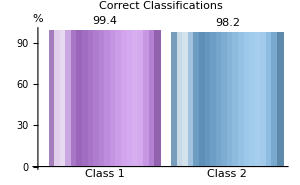

Test Set:

98.6% correct classifications

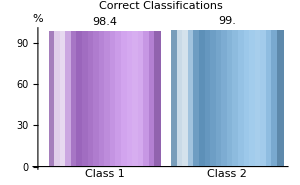

```mathematica
trainingFraction=0.5;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
perceptronTrainOptimization=CIP`Perceptron`GetPerceptronTrainOptimization[reducedWdbcDataSet,numberOfHiddenNeurons,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength->blackListLength];

bestOptimization="MinimumDeviation";
bestIndex=CIP`Perceptron`GetBestPerceptronClassOptimization[perceptronTrainOptimization,UtilityOptionsBestOptimization->bestOptimization];

trainingAndTestSet=perceptronTrainOptimization[[3,bestIndex]];
perceptronInfo=perceptronTrainOptimization[[4,bestIndex]];
CIP`Perceptron`ShowPerceptronClassificationResult[{"CorrectClassification","CorrectClassificationPerClass"},trainingAndTestSet,perceptronInfo]
```

Remarks:
Predictive success is slightly superior to 5-HN perceptron approach.

### 9 hidden neurons (9-HN)

```mathematica
numberOfHiddenNeurons=9;
```

#### Minimal set of input features

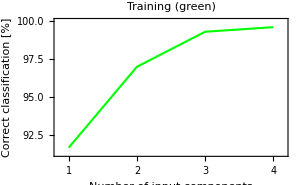

Input component list = {23,25,2,19}

```mathematica
trainingAndTestSet={wdbcDataSet,{}};
numberOfInclusionsPerStepList=Table[1,{4}];
perceptronInputComponentRelevanceListForClassification=CIP`Perceptron`GetPerceptronInputInclusionClass[trainingAndTestSet,numberOfHiddenNeurons,UtilityOptionsInclusionsPerStep->numberOfInclusionsPerStepList];
CIP`Perceptron`ShowPerceptronInputRelevanceClass[perceptronInputComponentRelevanceListForClassification]
```

```mathematica
inputComponentInclusionList={23,25,2,19};
reducedWdbcDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[wdbcDataSet,inputComponentInclusionList];
```

#### Training/test set partitioning for reduced WDBC data set

Training Set:

97.9% correct classifications

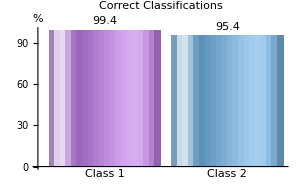

Test Set:

97.9% correct classifications

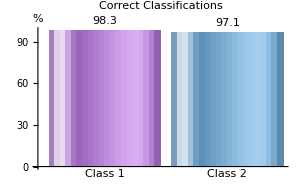

```mathematica
trainingFraction=0.5;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
perceptronTrainOptimization=CIP`Perceptron`GetPerceptronTrainOptimization[reducedWdbcDataSet,numberOfHiddenNeurons,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength->blackListLength];

bestOptimization="MinimumDeviation";
bestIndex=CIP`Perceptron`GetBestPerceptronClassOptimization[perceptronTrainOptimization,UtilityOptionsBestOptimization->bestOptimization];

trainingAndTestSet=perceptronTrainOptimization[[3,bestIndex]];
perceptronInfo=perceptronTrainOptimization[[4,bestIndex]];
CIP`Perceptron`ShowPerceptronClassificationResult[{"CorrectClassification","CorrectClassificationPerClass"},trainingAndTestSet,perceptronInfo]
```

Remarks:
Predictive success is slightly inferior to 5-HN and 7-HN and comparable to 3-HN perceptron approach.

## Discussion

Unsupervised Learning < Supervised Learning

MLR ≈ parabolic MPR < cubic MPR < 3-HN Perceptron < 5-HN Perceptron <  7-HN Perceptron >  9-HN Perceptron